## Matrix elements calculation

## a-> 4P

### 4π

#### Simplifications of the scalar products

```mathematica
ProductP1P24body4π=ProductP1P24body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}
ProductP1P34body4π=Assuming[s34>0&&s12>0,Simplify[Assuming[s34>4 mπ0^2&&mπ0>0,Simplify[ProductP1P34body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}]]]]/.{√((s12-4 mπ0^2) (s34-4 mπ0^2))->√s12 √s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s12 (s12-4 mπ0^2))->s12 √(1-(4 mπ0^2)/s12)}/.{√(s34 (s34-4 mπ0^2))->s34 √(1-(4 mπ0^2)/s34)}/.{√(s12-4 mπ0^2)->√s12 √(1-(4 mπ0^2)/s12)}/.{√(s34^5 (s34-4 mπ0^2))->s34^3 √(1-(4 mπ0^2)/s34)}/.{√(s12 s34 (s12-4 mπ0^2) (s34-4 mπ0^2))->s12*s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}//Simplify;
ProductP1P44body4π=Assuming[s34>0&&s12>0,Simplify[Assuming[s34>4 mπ0^2&&mπ0>0,Simplify[ProductP1P44body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}]]]]/.{√(s12 (s12-4 mπ0^2))->s12 √(1-(4 mπ0^2)/s12)}/.{√(s12 s34 (s12-4 mπ0^2) (s34-4 mπ0^2))->s12*s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s34 (s34-4 mπ0^2))->s34 √(1-(4 mπ0^2)/s34)}/.{√(s34^5 (s34-4 mπ0^2))->s34^3 √(1-(4 mπ0^2)/s34)}/.{√((s12-4 mπ0^2) (s34-4 mπ0^2))->√s12 √s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s12-4 mπ0^2)->√s12 √(1-(4 mπ0^2)/s12)}//Simplify;
ProductP2P34body4π=Assuming[s34>0&&s12>0,Simplify[Assuming[s34>4 mπ0^2&&mπ0>0,Simplify[ProductP2P34body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}]]]]/.{√((s12-4 mπ0^2) (s34-4 mπ0^2))->√s12 √s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s12 s34 (s12-4 mπ0^2) (s34-4 mπ0^2))->s12*s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s12 (s12-4 mπ0^2))->s12 √(1-(4 mπ0^2)/s12)}/.{√(s34 (s34-4 mπ0^2))->s34 √(1-(4 mπ0^2)/s34)}/.{√(s34^5 (s34-4 mπ0^2))->s34^3 √(1-(4 mπ0^2)/s34)}/.{√(s12-4 mπ0^2)->√s12 √(1-(4 mπ0^2)/s12)}//Simplify;
ProductP2P44body4π=(Assuming[s34>0&&s12>0,Simplify[Assuming[s34>4 mπ0^2&&mπ0>0,Simplify[ProductP2P44body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}]]]]/.{√((s12-4 mπ0^2)/s34)->(√s12)/(√s34)√(1-(4 mπ0^2)/s12)}/.{√(s34 (s34-4 mπ0^2))->s34 √(1-(4 mπ0^2)/s34)}/.{√(s12 (s12-4 mπ0^2))->s12 √(1-(4 mπ0^2)/s12)}/.{√(s34 (s34-4 mπ0^2) (ma^4-2 ma^2 (s12+s34)+(s12-s34)^2))->s34 √(1-(4 mπ0^2)/s34)√(ma^4-2 ma^2 (s12+s34)+(s12-s34)^2)}/.{√(s34 (4 mπ0^2-s12) (4 mπ0^2-s34))->s34 √s12 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s34 (s12-4 mπ0^2) (s34-4 mπ0^2))->s34 √s12 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)})//Simplify;
ProductP3P44body4π=Assuming[s34>0&&s12>0,Simplify[Assuming[s34>4 mπ0^2&&mπ0>0,Simplify[ProductP3P44body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}]]]];
Assuming[s34>4 mπ0^2&&s12>4 mπ0^2&&mπ0>0,Simplify[2*(ProductP1P24body4π+ProductP1P34body4π+ProductP1P44body4π+ProductP2P34body4π+ProductP2P44body4π+ProductP3P44body4π)+4 mπ0^2]];
```

1/2 (s12-2 mπ0^2)

#### Kinematics

```mathematica
particleslist["2π^+2π^-"]={"π^+","π^-","π^+","π^-"};
particleslist["π^+π^-2π^0"]={"π^+","π^0","π^-","π^0"};
proclist={"2π^+2π^-","π^+π^-2π^0"};
Do[
prgroupname[proc]="4π";
prclassname[proc]="Hadronic, ChPT";
,{proc,proclist}]
Do[intmethod[proc]="AdaptiveMonteCarlo",{proc,proclist}];
Sfactor["2π^+2π^-"]=1/4;
Sfactor["π^+π^-2π^0"]=1/2;
mLimitationMin["2π^+2π^-"]=mLimitationMin["π^+π^-2π^0"]=0;
(*Above 1.6 GeV, it will switch to 2ρ*)
mLimitationMax["2π^+2π^-"]=mLimitationMax["π^+π^-2π^0"]=1.6;
labelList["2π^+2π^-"]=labelList["π^+π^-2π^0"]={1,2,3,4};
momList["2π^+2π^-"]=momList["π^+π^-2π^0"]=Table[Symbol["p"<>(labelList["2π^+2π^-"][[i]]//ToString)],{i,1,Length[labelList["2π^+2π^-"]],1}]
rule4MomentumConservation[expr_,"2π^+2π^-"]:=ExpandScalarProduct[expr/.{pa->Total[momList["2π^+2π^-"]]}]
rule4MomentumConservation[expr_,"π^+π^-2π^0"]:=rule4MomentumConservation[expr,"2π^+2π^-"]
ruleScalarProducts[expr_,"2π^+2π^-"]:=(expr/.{ScalarProduct[momList["2π^+2π^-"][[1]],momList["2π^+2π^-"][[1]]]->mπ0^2,ScalarProduct[momList["2π^+2π^-"][[2]],momList["2π^+2π^-"][[2]]]->mπ0^2,ScalarProduct[momList["2π^+2π^-"][[3]],momList["2π^+2π^-"][[3]]]->mπ0^2,ScalarProduct[momList["2π^+2π^-"][[4]],momList["2π^+2π^-"][[4]]]->mπ0^2,ScalarProduct[momList["2π^+2π^-"][[1]],momList["2π^+2π^-"][[2]]]->ProductP1P24body4π,ScalarProduct[momList["2π^+2π^-"][[1]],momList["2π^+2π^-"][[3]]]->ProductP1P34body4π,ScalarProduct[momList["2π^+2π^-"][[1]],momList["2π^+2π^-"][[4]]]->ProductP1P44body4π,ScalarProduct[momList["2π^+2π^-"][[2]],momList["2π^+2π^-"][[3]]]->ProductP2P34body4π,ScalarProduct[momList["2π^+2π^-"][[2]],momList["2π^+2π^-"][[4]]]->ProductP2P44body4π,ScalarProduct[momList["2π^+2π^-"][[3]],momList["2π^+2π^-"][[4]]]->ProductP3P44body4π})/.{m->ma,m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0}
ruleScalarProducts[expr_,"π^+π^-2π^0"]:=ruleScalarProducts[expr,"2π^+2π^-"]
```

{p1,p2,p3,p4}

#### Matrix elements

```mathematica
ResourceFunction["MonitorProgress"]@Do[
M4body[proc,"Contact"]=Mdecayalp["No off-shell",particleslist[proc],labelList[proc]];
M4body[proc,"VMD"]=MDecayalp["V off-shell 4-body","ρ^0","ρ^0",particleslist[proc],labelList[proc]]+MDecayalp["V off-shell 4-body","ρ^+","ρ^-",particleslist[proc],labelList[proc]];
M4body[proc,"Total"]=M4body[proc,"Contact"]+M4body[proc,"VMD"];
M4bodyStar[proc,"Total"]=M4body[proc,"Total"]/.{I->-I};
M2symbolic4body[proc]=ruleKinematics[(M4body[proc,"Total"]//Simplify)(M4bodyStar[proc,"Total"]//Simplify)//Contract,proc];
M2numeric4body[proc,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_,s12_,s34_,θ1_,θ3_,ϕ3_]=Ffunction[ma]^2*symbolsToNumbersWidths[ruleKinematics[M2symbolic4body[proc],proc]];
M2numericSM4body["η'",proc,s12_,s34_,θ1_,θ3_,ϕ3_]=ruleSymbolsToNumbers[ruleKinematics[M2symbolic4body[proc],proc],"ALP is η'",0]/.{fa->Fπ,ma->MASS["η'"],cu->0,cd->0,cs->0,cG->0};
,{proc,proclist}]//AbsoluteTiming
Print["Contact terms (are zero due to the flavor symmetry for this decay):"]
M4body["2π^+2π^-","Contact"]
M4body["π^+π^-2π^0","Contact"]
Print["VMD terms:"]
M4body["2π^+2π^-","VMD"]
M4body["π^+π^-2π^0","VMD"]
```

{6.11315,Null}

Contact terms (are zero due to the flavor symmetry for this decay):

0

0

VMD terms:

(mρplus^4 ϵ (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4]) (3 cG coef1 (κd+κu)+√6 ηALP+√3 ηprALP))/(8 π^2 fπ^5 ((ⅈ Γρ0 mρ0^2 ((2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2-4 mπ0^2)/(mρ0^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2))+2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2-mρ0^2) ((ⅈ Γρ0 mρ0^2 ((2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2-4 mπ0^2)/(mρ0^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2))+2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2-mρ0^2))-(mρplus^4 ϵ (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4]) (3 cG coef1 (κd+κu)+√6 ηALP+√3 ηprALP))/(8 π^2 fπ^5 ((ⅈ Γρ0 mρ0^2 ((2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2-4 mπ0^2)/(mρ0^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2))+2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2-mρ0^2) ((ⅈ Γρ0 mρ0^2 ((2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2-4 mπ0^2)/(mρ0^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2))+2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2-mρ0^2))

(mρplus^4 ϵ (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4]) (3 cG coef1 (κd+κu)+√6 ηALP+√3 ηprALP))/(8 π^2 fπ^5 ((ⅈ Γρplus mρplus^2 ((2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2-4 mπ0^2)/(mρplus^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2))+2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2-mρplus^2) ((ⅈ Γρplus mρplus^2 ((2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2-4 mπ0^2)/(mρplus^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2))+2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2-mρplus^2))-(mρplus^4 ϵ (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4]) (3 cG coef1 (κd+κu)+√6 ηALP+√3 ηprALP))/(8 π^2 fπ^5 ((ⅈ Γρplus mρplus^2 ((2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2-4 mπ0^2)/(mρplus^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2))+2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2-mρplus^2) ((ⅈ Γρplus mρplus^2 ((2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2-4 mπ0^2)/(mρplus^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2))+2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2-mρplus^2))

Width of η'->4π in eV (compare to the result obtained in https://arxiv.org/pdf/1111.5949.pdf (3.3*10^-4*0.199 MeV = 66 eV):

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 8.96973×10^-8+6.93236×10^-26 ⅈ and 1.46515×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 9.45759×10^-8-4.2548×10^-26 ⅈ and 1.56357×10^-9 for the integral and error estimates.

69.7123

#### Cross-check

Width of η’→4π

```mathematica
Print["Width of η'->4π in eV (compare to the result obtained in https://arxiv.org/pdf/1111.5949.pdf (3.3*10^-4*0.199 MeV = 66 eV):"]
 (ΓnumericSM["η'","2π^+2π^-"]+ΓnumericSM["η'","π^+π^-2π^0"])*10^9
```

κ-independence

```mathematica
xxx=M4body["2π^+2π^-","VMD"]/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
D[xxx,κu]κu+D[xxx,κd]κd//Simplify
```

1/(8 π^2 fπ^5)3 cG (coef1-1) mρplus^4 ϵ (κd+κu) (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4]) (1/(((ⅈ Γρ0 mρ0^2 ((2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2-4 mπ0^2)/(mρ0^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2))+2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2-mρ0^2) ((ⅈ Γρ0 mρ0^2 ((2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2-4 mπ0^2)/(mρ0^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2))+2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2-mρ0^2))-1/(((ⅈ Γρ0 mρ0^2 ((2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2-4 mπ0^2)/(mρ0^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2))+2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2-mρ0^2) ((ⅈ Γρ0 mρ0^2 ((2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2-4 mπ0^2)/(mρ0^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2))+2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2-mρ0^2)))

## a->3π

### Definitions

```mathematica
particleslist["3π^0"]={"π^0","π^0","π^0"};
particleslist["π^+π^-π^0"]={"π^+","π^-","π^0"};
prgroupname["3π^0"]=prgroupname["π^+π^-π^0"]="3π";
prclassname["3π^0"]=prclassname["π^+π^-π^0"]="Hadronic, ChPT";
Sfactor["3π^0"]=1/(3!);
Sfactor["π^+π^-π^0"]=1;
mLimitationMin["3π^0"]=mLimitationMin["π^+π^-π^0"]=0;
mLimitationMax["3π^0"]=mLimitationMax["π^+π^-π^0"]=3;
labelList["3π^0"]=labelList["π^+π^-π^0"]={π1,π2,π3};
momList["3π^0"]=momList["π^+π^-π^0"]=Table[Symbol["p"<>(labelList["3π^0"][[i]]//ToString)],{i,1,Length[labelList["3π^0"]],1}]
rule4MomentumConservation[expr_,"π^+π^-π^0"]:=ExpandScalarProduct[expr/.{pa->Total[momList["3π^0"]]}]
rule4MomentumConservation[expr_,"3π^0"]:=rule4MomentumConservation[expr,"π^+π^-π^0"]
ruleScalarProducts[expr_,"π^+π^-π^0"]:=expr/.Flatten[Table[ScalarProduct[momList["3π^0"][[i]],momList["3π^0"][[j]]]->ScalarProduct3body[i,j],{i,1,3,1},{j,i,3,1}]]/.{m->ma,m1->mπ0,m2->mπ0,m3->mπ0}
ruleScalarProducts[expr_,"3π^0"]:=ruleScalarProducts[expr,"π^+π^-π^0"]
```

{pπ1,pπ2,pπ3}

### Pure π^0 mixing part - validation by comparing with https://arxiv.org/pdf/2012.12272.pdf, Eqs. 106

```mathematica
Print["Contact Lagrangian 3πa (assuming only mixing with π^0):"]
Lagrangian2πchπ0aOnlyπ0Mixing=LagrangianGivenFields[{"a","π^0","π^+","π^-"},{1,1,1,1}]/.Evaluate[rulem0aTransformationSymbolicToExplicit["Only π^0a"]]/.{cvmd->0}//Expand//Simplify;
Lagrangian3π0aOnlyπ0Mixing=LagrangianGivenFields[{"a","π^0"},{1,3}]/.Evaluate[rulem0aTransformationSymbolicToExplicit["Only π^0a"]]/.{cvmd->0}//Expand//Simplify;
Lagrangian2πchπ0aOnlyπ0Mixing+Lagrangian3π0aOnlyπ0Mixing//Simplify
(*Keeping only 4-field terms*)
Print["Matrix element a->3π^0 in the leading order in isospin breaking parameter δ:"]
Mato3π0Onlyπ0Mixing=ruleKinematics[Mdecayalp["No off-shell",particleslist["3π^0"],labelList["3π^0"]],"3π^0"]/.Evaluate[rulem0aTransformationSymbolicToExplicit["Only π^0a"]]/.{cvmd->0,κd->1-κu}//Together//Simplify
(*Mato3π0Onlyπ0Mixing=ruleKinematics[FeynmanRuleVertex[Lagrangian3πaOnlyπ0Mixing,"a","π^0","π^0","π^0","Null",1,-1,-1,-1,0],"3π"]*)
Print["Matrix element a->π^+π^-π^0 in the leading order in isospin breaking parameter δ:"]
Matoπpπmπ0Onlyπ0Mixing=(*ruleKinematics[FeynmanRuleVertex[Lagrangian3πaOnlyπ0Mixing,"a","π^+","π^-","π^0","Null",1,-1,-1,-1,0],"3π"]*)ruleKinematics[Mdecayalp["No off-shell",particleslist["π^+π^-π^0"],labelList["π^+π^-π^0"]],"π^+π^-π^0"]/.Evaluate[rulem0aTransformationSymbolicToExplicit["Only π^0a"]]/.{cvmd->0,κd->1-κu}//Together//Simplify
Print["Differential decay widths dΓ/dm_ππ assuming m_a < m_η':"]
dΓato3π0dm12[xx_]=1/(2*Pi)^3 1/(32 ma^3)Integrate[Refine[Mato3π0Onlyπ0Mixing,ma<mηpr]^2,{m23,m23lower[m12,ma,mπ0,mπ0,mπ0],m23upper[m12,ma,mπ0,mπ0,mπ0]}]//Expand//Simplify
dΓatoπpπmπ0dm12[xx_]=1/(2*Pi)^3 1/(32 ma^3)1/(3!)Integrate[Refine[Matoπpπmπ0Onlyπ0Mixing,ma<mηpr]^2,{m23,m23lower[m12,ma,mπ0,mπ0,mπ0],m23upper[m12,ma,mπ0,mπ0,mπ0]}]//Expand//Simplify
```

Contact Lagrangian 3πa (assuming only mixing with π^0):

1/(6 fπ^2 (ma^2-mπ0^2))ϵ (ma^2 mπ0^2 alp(x) (π0(x))^3 (cd-cG δ (κd+κu)-cu)-2 (alp(x) (dπminus(x,μ) (2 π0(x) dπplus(x,μ)-πplus(x) dπ0(x,μ)) (cd ma^2+cG ma^2 (κd-κu)-cG mπ0^2 ((δ+1) κd+(δ-1) κu)-cu ma^2)+πminus(x) (dπ0(x,μ) dπplus(x,μ) (-cd ma^2+cG ma^2 (κu-κd)+cG mπ0^2 ((δ+1) κd+(δ-1) κu)+cu ma^2)+ma^2 mπ0^2 π0(x) πplus(x) (-cd+cG δ (κd+κu)+cu)))+dalp(x,μ) (cd (ma^2-2 mπ0^2)+cG ma^2 (κd-κu)+cG mπ0^2 ((δ-1) κd+(δ+1) κu)-cu (ma^2-2 mπ0^2)) (πplus(x) (π0(x) dπminus(x,μ)-2 πminus(x) dπ0(x,μ))+π0(x) πminus(x) dπplus(x,μ))))

Matrix element a->3π^0 in the leading order in isospin breaking parameter δ:

(ma^2 mπ0^2 ϵ (cd-cG δ-cu))/(fπ^2 (ma^2-mπ0^2))

Matrix element a->π^+π^-π^0 in the leading order in isospin breaking parameter δ:

(mπ0^2 ϵ (mπ0^2-m12) (cd-cG δ-cu))/(fπ^2 (mπ0^2-ma^2))

Differential decay widths dΓ/dm_ππ assuming m_a < m_η':

(ma mπ0^4 ϵ^2 √(m12-4 mπ0^2) √(((ma^2-mπ0^2)^2)/m12+m12-2 (ma^2+mπ0^2)) (-cd+cG δ+cu)^2)/(256 π^3 fπ^4 (ma^2-mπ0^2)^2)

(mπ0^4 ϵ^2 √(m12-4 mπ0^2) (m12-mπ0^2)^2 √(((ma^2-mπ0^2)^2)/m12+m12-2 (ma^2+mπ0^2)) (-cd+cG δ+cu)^2)/(1536 π^3 fπ^4 ma^3 (ma^2-mπ0^2)^2)

### All mesons included

```mathematica
ResourceFunction["MonitorProgress"]@Do[
Msymbolic[process,"Pure ChPT"]=UnitStep[mηpr-ma] √kfact(ruleKinematics[Mdecayalp["No off-shell",particleslist[process],labelList[process]]/.{cvmd->0},process]//Expand)/.{G8->0}//Simplify;
Msymbolic[process,"VMD contact"]=ruleKinematics[(Mdecayalp["Pure ChPT",particleslist[process],labelList[process]]-(Mdecayalp["Pure ChPT",particleslist[process],labelList[process]]/.{cvmd->0}))/.{cvmd->1,G8->0}//Simplify,process]//Simplify;
Msymbolic[process,"T off-shell"]=ruleKinematics[MDecayalp["T off-shell",particleslist[process],labelList[process]],process];
Msymbolic[process,"V off-shell"]=ruleKinematics[MDecayalp["V off-shell 3-body no vector",particleslist[process],labelList[process]],process];
Msymbolic[process,"S off-shell"]=ruleKinematics[MDecayalp["S off-shell",particleslist[process],labelList[process]],process];
sublist=Select[Keys[DownValues@Msymbolic][[All,1,2]]//DeleteDuplicates,#!="Total"&];
Do[
(*If[sub!="No off-shell",Msymbolic[process,sub]=Sum[Msymbolic[process,sub][[i]]//Simplify,{i,1,Length[Msymbolic[process,sub]],1}]];*)
MsymbolicStar[process,sub]=Refine[Conjugate[Msymbolic[process,sub]]//ComplexExpand,kfact>0],{sub,sublist}];
Msymbolic3body[process,"Total"]=Sum[Msymbolic[process,sub],{sub,sublist}];
MsymbolicStar3body[process,"Total"]=Sum[MsymbolicStar[process,sub],{sub,sublist}];
M2symbolic3body[process]=Msymbolic3body[process,"Total"]*MsymbolicStar3body[process,"Total"];
M2numeric3body[process,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_,m12_,m23_]=(symbolsToNumbersWidths3π[M2symbolic3body[process]]/.{kfact->2.7})*Ffunction[ma]^2;
M2numericSM3body["η'",process,m12_,m23_]=ruleSymbolsToNumbers[M2symbolic3body[process],"ALP is η'",2]/.{cu->0,cd->0,cs->0,cG->0,ma->MASS["η'"],fa->Fπ}/.{kfact->2.7};
,{process,{"3π^0","π^+π^-π^0"}}]//AbsoluteTiming
```

{47.6641,Null}

#### Cross-checks

1. Symbolic expression matches 1811.03474 for the standard choice of κ_q = (m^-1)_q/(Σ_q(m^-1)_q)

```mathematica
Print["Matrix element for the process a→3π^0: difference between the expression obtained in this notebook and the one from 1811.03474"]
Mato3π0Soreq=√kfact(mπ0^2*ϵ)/fπ^2(π0ALP-δ(1/(√3)+√2 ηπ0+ηprπ0)(√2 ηALP+ηprALP)+(√3)/2 δ(√2 ηπ0+ηprπ0));
xxx=Refine[Msymbolic["3π^0","Pure ChPT"],ma<mηpr]/.{cu->0,cd->0,cs->0,cG->-1/2};
xxx=Normal@Series[xxx/.{κu->Simplify[κmatrixStandard[[1]][[1]]],κd->Simplify[κmatrixStandard[[2]][[2]]]}/.{mu->muδsol}//Simplify,{δ,0,1},{md,0,0}]//Simplify;
xxx-Mato3π0Soreq//Expand
Print["Matrix element for the process a→π^+π^-π^0: difference between the expression obtained in this notebook and the one from 1811.03474"]
Mato2πchπ0Soreq=ϵ/(3 fπ^2)√kfact(π0ALP(3m12-ma^2-2 mπ0^2)-mπ0^2 δ(1/(√3)+√2 ηπ0+ηprπ0)(√2 ηALP+ηprALP)+δ/2(√3 mπ0^2(√2 ηπ0+ηprπ0)-3m12+ma^2+3 mπ0^2));
xxx=Refine[Msymbolic["π^+π^-π^0","Pure ChPT"],ma<mηpr]/.{cu->0,cd->0,cs->0,cG->-1/2};
xxx=Normal@Series[xxx/.{κu->Simplify[κmatrixStandard[[1]][[1]]],κd->Simplify[κmatrixStandard[[2]][[2]]]}/.{mu->muδsol}//Simplify,{δ,0,1},{md,0,0}]//Simplify;
xxx-Mato2πchπ0Soreq//Expand//Simplify
```

Matrix element for the process a→3π^0: difference between the expression obtained in this notebook and the one from 1811.03474

0

Matrix element for the process a→π^+π^-π^0: difference between the expression obtained in this notebook and the one from 1811.03474

0

0

2. The pure ChPT part of the matrix element is actually κ-independent after inserting the expressions for the mixing angles

```mathematica
proc="S off-shell";
melement1=Refine[Msymbolic["π^+π^-π^0",proc],ma<mηpr];
melement1=melement1/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
Print["Decay into π^+π^-π^0 - the part ~(#κ)_u+(#κ)_d:"]
D[melement1,κu]κu+D[melement1,κd]κd/.{coef1->1}//Expand
melement1=Refine[Msymbolic["3π^0",proc],ma<mηpr];
melement1=melement1/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
Print["Decay into 3π^0 - the part ~(#κ)_u+(#κ)_d:"]
D[melement1,κu]κu+D[melement1,κd]κd/.{coef1->1}//Expand
```

Decay into π^+π^-π^0 - the part ~(#κ)_u+(#κ)_d:

0

Decay into 3π^0 - the part ~(#κ)_u+(#κ)_d:

0

## a->η(η')PP: ηππ, η’ππ, 3η

### Kinematics

```mathematica
prlist={"η2π^0","ηπ^+π^-","η'π^+π^-","η'2π^0","3η"};
Do[prgroupname[pr]="η2π",{pr,{"η2π^0","ηπ^+π^-"}}];
Do[prgroupname[pr]="η'2π",{pr,{"η'2π^0","η'π^+π^-"}}];
Do[prgroupname[pr]="3η",{pr,{"3η"}}];
Do[prclassname[pr]="Hadronic, ChPT",{pr,prlist}];
particleslist["η2π^0"]={"η","π^0","π^0"};
particleslist["ηπ^+π^-"]={"η","π^+","π^-"};
particleslist["η'π^+π^-"]={"η'","π^+","π^-"};
particleslist["η'2π^0"]={"η'","π^0","π^0"};
particleslist["3η"]={"η","η","η"};
Sfactor["η2π^0"]=Sfactor["η'2π^0"]=1/2;
Sfactor["ηπ^+π^-"]=Sfactor["η'π^+π^-"]=1;
Sfactor["3η"]=1/(3!);
labelList["η2π^0"]=labelList["ηπ^+π^-"]={"η","π1","π2"};
labelList["η'2π^0"]=labelList["η'π^+π^-"]={"ηpr","π1","π2"};
labelList["3η"]={"η1","η2","η3"};
Do[
mLimitationMin[proc]=0;
mLimitationMax[proc]=3;
momList[proc]=Symbol["p"<>(#//ToString)]&/@labelList[proc]
,{proc,prlist}]
Table[With[{proc=proc},
rule4MomentumConservation[expr_,proc]:=ExpandScalarProduct[expr/.{pa->Total[momList[proc]]}];
ruleScalarProducts[expr_,proc]:=expr/.Flatten[Table[ScalarProduct[momList[proc][[i]],momList[proc][[j]]]->ScalarProduct3body[i,j],{i,1,3,1},{j,i,3,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[proc][[i]]],{i,1,3,1}];]
,{proc,prlist}]
```

{Null,Null,Null,Null,Null}

### Matrix elements

```mathematica
Print["ηALP2π Lagrangians (pure ChPT terms) - ηπ^+π^-:"]
(*Leaving only terms with 1 eta*)
Lagrangianη2πchaSymbolic=(LagrangianGivenFields[{"a","η","π^+","π^-"},{1,1,1,1}])/.{md->0}//Expand//Simplify
Print["ηALP2π Lagrangians (pure ChPT terms) - η2π^0:"]
Lagrangianη2π0aSymbolic=(LagrangianGivenFields[{"a","η","π^0"},{1,1,2}])/.{md->0}//Expand//Simplify
Print["ηALP2π Lagrangians (pure ChPT terms) - 3η:"]
Lagrangian3ηaSymbolic=Normal@Series[LagrangianGivenFields[{"a","η"},{1,3}],{md,0,0}]//Expand//Simplify
ResourceFunction["MonitorProgress"]@Do[
Msymbolic3body[process,"Pure ChPT"]=(*UnitStep[mηpr-ma]*)(ruleKinematics[Mdecayalp["No off-shell",particleslist[process],labelList[process]],process]//Expand)/.{cvmd->0}//Simplify;
Msymbolic3body[process,"f_2-mediated"]=ruleKinematics[MDecayalp["T off-shell","f_2",particleslist[process],labelList[process]],process];
Msymbolic3body[process,"S-mediated"]=ruleKinematics[MDecayalp["S off-shell",particleslist[process],labelList[process]],process];
sublistηππ={"Pure ChPT","f_2-mediated","S-mediated"};
Do[
MsymbolicStar3body[process,contr]=Msymbolic3body[process,contr]/.Flatten[Table[{I*Γsymbolic[mes]->-I*Γsymbolic[mes],-I*Γsymbolic[mes]->I*Γsymbolic[mes]},{mes,listMesonVPST}]],{contr,sublistηππ}];
Msymbolic3body[process,"Total"]=Sum[Msymbolic3body[process,contr],{contr,sublistηππ}];
MsymbolicStar3body[process,"Total"]=Sum[MsymbolicStar3body[process,contr],{contr,sublistηππ}];
M2symbolic3body[process]=Msymbolic3body[process,"Total"]*MsymbolicStar3body[process,"Total"];
(*The value of the Subscript[θ, η] corresponds to the choice made in https://arxiv.org/pdf/hep-ph/9902238.pdf*)
M2numeric3body[process,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_,m12_,m23_]=symbolsToNumbersWidths[M2symbolic3body[process]]*Ffunction[ma]^2;
M2numericSM3body["η'",process,m12_,m23_]=ruleSymbolsToNumbers[M2symbolic3body[process]/.{κu->0,κd->0},"ALP is η'",0]/.{cu->0,cd->0,cs->0,cG->0,ma->MASS["η'"],fa->Fπ}
,{process,{"3η","η2π^0","ηπ^+π^-","η'2π^0","η'π^+π^-"}}]//AbsoluteTiming
```

ηALP2π Lagrangians (pure ChPT terms) - ηπ^+π^-:

1/(18 fπ^2)ϵ (alp(x) (3 δ ηπ0 dπminus(x,μ) (2 η(x) dπplus(x,μ)-πplus(x) dη(x,μ)) (3 cvmd mηpr-ma (cG (κu-κd)+π0ALP)-2 π0ALP)+πminus(x) (3 δ ηπ0 dη(x,μ) dπplus(x,μ) (3 cvmd mηpr-ma (cG κd-cG κu-π0ALP)+2 π0ALP)+2 mπ0^2 η(x) πplus(x) (-3 cG δ ηπ0 κd+3 cG δ ηπ0 κu+3 √6 cG δ κd-3 √6 cG δ κu+3 √6 cG κd+3 √6 cG κu+3 δ ηπ0 π0ALP-√6 δ π0ALP+6 ηALP+3 √2 ηprALP)))-3 δ ηπ0 dalp(x,μ) (πplus(x) (η(x) dπminus(x,μ)-2 πminus(x) dη(x,μ))+η(x) πminus(x) dπplus(x,μ)) (4 cd-2 (-2 cG κd+2 cG κu+2 cu+π0ALP)+3 cvmd mηpr-ma (cG (κu-κd)+π0ALP)))

ηALP2π Lagrangians (pure ChPT terms) - η2π^0:

(mπ0^2 ϵ alp(x) η(x) (π0(x))^2 (cG δ ηπ0 κd-cG δ ηπ0 κu+2 √2 cG δ ηprπ0 κd-2 √2 cG δ ηprπ0 κu+√6 cG δ κd-√6 cG δ κu+√6 cG κd+√6 cG κu-δ ηπ0 π0ALP-2 √2 δ ηprπ0 π0ALP-√6 δ π0ALP+2 ηALP+√2 ηprALP))/(6 fπ^2)

ηALP2π Lagrangians (pure ChPT terms) - 3η:

(mπ0^2 ϵ alp(x) (η(x))^3 (cG (κd md (δ (√6-9 ηπ0)+√6)+κu md (9 δ ηπ0-√6 δ+√6)+√6 (δ+1) ms (κd+κu-1))+md (9 δ ηπ0 π0ALP-√6 δ π0ALP+2 ηALP+√2 ηprALP)+(δ+1) ms (ηALP-√2 ηprALP)))/(27 fπ^2 md)

{38.6135,Null}

#### Cross-checks

1. Symbolic expression matches 1811.03474 for the standard choice of κ_q = (m^-1)_q/(Σ_q(m^-1)_q)

```mathematica
proc="Pure ChPT";
Print["Matrix element for a→η2π^0 (for comparison with 1811.03474):"]
Msymbolic3body["η2π^0","Pure ChPT"]/.{md->0,cu->0,cd->0,cs->0,δ->0,cG->cG}//Simplify
Print["Matrix element for a→ηπ^+π^- (for comparison with 1811.03474):"]
Msymbolic3body["ηπ^+π^-","Pure ChPT"]/.{md->0,cu->0,cd->0,cs->0,δ->0,cG->cG}//Simplify
Print["Matrix element for a→ηππ - expression from 1811.03474:"]
Matoeta2πmixingSoreq=ϵ mπ0^2/(3 fπ^2)(√2(eta0/.etasols)+(eta8/.etasols))/.{md->0,δ^2->0,cu->0,cd->0,cs->0,cG->0,ctheta->Cos[θηStandard],stheta->Sin[θηStandard]}//Simplify
```

Matrix element for a→η2π^0 (for comparison with 1811.03474):

(mπ0^2 ϵ (√6 cG (κd+κu)+2 ηALP+√2 ηprALP))/(3 fπ^2)

Matrix element for a→ηπ^+π^- (for comparison with 1811.03474):

(mπ0^2 ϵ (√6 cG (κd+κu)+2 ηALP+√2 ηprALP))/(3 fπ^2)

Matrix element for a→ηππ - expression from 1811.03474:

(mπ0^2 ϵ (√2 η(x)+ηpr(x)))/(3 fπ^2)

2. The pure ChPT part of the matrix element is actually κ-independent after inserting the expressions for the mixing angles

```mathematica
contribution={"Pure ChPT","f_2-mediated","S-mediated"}[[1]];
melement1=Refine[Msymbolic3body["η2π^0",contribution],ma<mηpr];
melement1=melement1/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
Print["Decay into η2π^0 - the part ~(#κ)_u+(#κ)_d:"]
D[melement1,κu]κu+D[melement1,κd]κd/.{coef1->1}//Expand
melement1=Refine[Msymbolic3body["ηπ^+π^-",contribution],ma<mηpr];
melement1=melement1/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
Print["Decay into ηπ^+π^- - the part ~(#κ)_u+(#κ)_d:"]
D[melement1,κu]κu+D[melement1,κd]κd/.{mπplus->mπ0}/.{coef1->1}//Simplify
```

Decay into η2π^0 - the part ~(#κ)_u+(#κ)_d:

0

Decay into ηπ^+π^- - the part ~(#κ)_u+(#κ)_d:

0

3. Computation of the decay width η’->η2π

```mathematica
Print["Numeric value of the η'→η2π width in MeV (according to pdf, should be 0.188 MeV*0.(42+0.22) ~ 0.12 MeV):"]
(ΓnumericSM["η'","ηπ^+π^-"]+ΓnumericSM["η'","η2π^0"])*10^3
```

Numeric value of the η'→η2π width in MeV (according to pdf, should be 0.188 MeV*0.(42+0.22) ~ 0.12 MeV):

0.102557

## a->γππ

### Kinematics

```mathematica
pr1="γπ^+π^-";
particleslist[pr1]={"π^+","π^-","A"};
prgroupname["γπ^+π^-"]="γππ";
prclassname["γπ^+π^-"]="Hadronic, ChPT";
Sfactor[pr1]=1;
mLimitationMin[pr1]=0;
mLimitationMax[pr1]=3;
labelList[pr1]={π1,π2,γ};
momList[pr1]=Table[Symbol["p"<>(labelList[pr1][[i]]//ToString)],{i,1,Length[labelList[pr1]],1}]
rule4MomentumConservation[expr_,pr1]:=ExpandScalarProduct[expr/.{pa->Total[momList[pr1]]}]
ruleScalarProducts[expr_,pr1]:=expr/.Flatten[Table[ScalarProduct[momList[pr1][[i]],momList[pr1][[j]]]->ScalarProduct3body[i,j],{i,1,3,1},{j,i,3,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[pr1][[i]]],{i,1,3,1}]
```

{pπ1,pπ2,pγ}

### Matrix element

```mathematica
γl=labelList[pr1][[Position[particleslist[pr1],"A"][[1]][[1]]]];
Msymbolic3body[pr1,"V off-shell γmm"]=MDecayalp["V off-shell γmm",particleslist[pr1],labelList[pr1]];
MsymbolicStar3body[pr1,"V off-shell γmm"]=ComplexConjugate[Msymbolic3body[pr1,"V off-shell γmm"]];
M2symbolic3body[pr1]=ruleKinematics[DoPolarizationSums[Msymbolic3body[pr1,"V off-shell γmm"]*MsymbolicStar3body[pr1,"V off-shell γmm"],Evaluate[Symbol["p"<>(γl//ToString)]]]//Contract,pr1]//ComplexExpand//Simplify;
M2numeric3body[pr1,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_,m12_,m23_]=symbolsToNumbersWidths[M2symbolic3body[pr1]]*Ffunction[ma]^2;//AbsoluteTiming
M2numericSM3body["η'",pr1,m12_,m23_]=ruleSymbolsToNumbers[M2symbolic3body[pr1]/.{κu->0,κd->0},"ALP is η'",0]/.{ma->MASS["η'"],fa->Fπ,cq->0,cG->0};
```

{0.0248388,Null}

#### Cross-checks

Calculation of the η'→γπ^+π^- width

```mathematica
Print["η'→γπ^+π^- decay width in MeV (according to pdg, should be ~0.055 MeV):"]
ΓnumericSM["η'","γπ^+π^-"]*10^3
```

η'→γπ^+π^- decay width in MeV (according to pdg, should be ~0.055 MeV):

0.0597142

κ dependence of the matrix element

```mathematica
expr00=Msymbolic3body[pr1,"V off-shell γmm"]/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
expr11=Msymbolic3body[pr1,"V off-shell γmm"]/.{cG->0}/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
D[expr00,κu]κu+D[expr00,κd]κd//Simplify
Print["If not using κ-covariant VMD Lagrangian:"]
D[expr11,κu]κu+D[expr11,κd]κd//Simplify
```

0

If not using κ-covariant VMD Lagrangian:

-(√αEM cG mρplus^2 ϵ (κd+2 κu) (ϵ̄)^(OverBar[pγ]OverBar[pπ1]OverBar[pπ2]ε̄(pγ)))/(2 π^(3/2) fπ^3 (2 (OverBar[pπ1]·OverBar[pπ2])+OverBar[pπ1]^2+OverBar[pπ2]^2-mρ0^2+ⅈ Γρ0 mρ0))

## a->KKπ

### Kinematics

```mathematica
particleslist["K^0(K̄)^0π^0"]={"K^0","(K̄)^0","π^0"};
particleslist["K^+K^-π^0"]={"K^+","K^-","π^0"};
particleslist["K^+(K̄)^0π^-"]={"K^+","(K̄)^0","π^-"};
particleslist["K^-K^0π^+"]={"K^-","K^0","π^+"};
proclistKKπ={"K^0(K̄)^0π^0","K^+K^-π^0","K^+(K̄)^0π^-","K^-K^0π^+"};
Do[
prgroupname[proc]="KKπ";
prclassname[proc]="Hadronic, ChPT";
,{proc,proclistKKπ}];
Do[
labelList[proc]={"K1","K2","π"};
Sfactor[proc]=1;
mLimitationMin[proc]=0;
mLimitationMax[proc]=3;
momList[proc]=Symbol["p"<>(#//ToString)]&/@labelList[proc]
,{proc,proclistKKπ}]
Table[With[{proc=proc},
rule4MomentumConservation[expr_,proc]:=ExpandScalarProduct[expr/.{pa->Total[momList[proc]]}];
ruleScalarProducts[expr_,proc]:=expr/.Flatten[Table[ScalarProduct[momList[proc][[i]],momList[proc][[j]]]->ScalarProduct3body[i,j],{i,1,3,1},{j,i,3,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[proc][[i]]],{i,1,3,1}];]
,{proc,proclistKKπ}]
```

{Null,Null,Null,Null}

### Matrix elements

#### K^*(1430) from BaBar data (using 2110.10691 but replacing in terms of κ-invariant quantities)

Coefficients

```mathematica
Coefκ0K0ALPsymbolic=(LagrangianGivenFields[{"κ^0","(K̄)^0","a"},{1,1,1}]//Simplify)/(κ0[x]*dalp[x,μ]*dK0bar[x,μ]);
CoefκminusKplusALPsymbolic=CoefκplusKminusALPsymbolic=(LagrangianGivenFields[{"κ^-","K^+","a"},{1,1,1}]//Simplify)/(κminus[x]*dKplus[x,μ]*dalp[x,μ]);
Coefκ0K0π0symbolic=(LagrangianGivenFields[{"κ^0","(K̄)^0","π^0"},{1,1,1}]//Simplify)/(κ0[x]*dπ0[x,μ]*dK0bar[x,μ])/.{δ->0};
Coefκ0Kplusπminussymbolic=(LagrangianGivenFields[{"κ^0","K^-","π^+"},{1,1,1}]//Simplify)/(κ0[x]*dπplus[x,μ]*dKminus[x,μ])/.{δ->0};
CoefκminusKplusπ0symbolic=(LagrangianGivenFields[{"κ^+","K^-","π^0"},{1,1,1}]//Simplify)/(κplus[x]*dπ0[x,μ]*dKminus[x,μ])/.{δ->0};
CoefκminusK0πplussymbolic=(LagrangianGivenFields[{"κ^+","(K̄)^0","π^-"},{1,1,1}]//Simplify)/(κplus[x]*dπminus[x,μ]*dK0bar[x,μ])/.{δ->0};
```

Matrix elements

```mathematica
tabDataBaBar={{0.67,0.154, 3.786},{0.73,0.198, 3.944},{0.79,0.161,1.634},{0.85,0.125, 3.094},{0.91,0.307,0.735},{0.97,0.528,−0.083},{1.03,0.215,0.541},{1.09,0.390,0.254},{1.15,0.490,0.618},{1.21,0.422,0.723},{1.27,0.581,0.605},{1.33,0.643,1.330},{1.39,0.920,1.528},{1.45,1.000,1.570},{1.51,0.750,1.844},{1.57,0.585, 2.128},{1.63,0.366, 2.389},{1.69,0.312,1.962},{1.75,0.427,1.939},{1.81,0.511, 2.426},{1.87,0.588, 2.242},{1.93,0.729, 2.427},{1.99,0.777, 2.306},{2.05,0.775, 2.347},{2.11,0.830, 2.374},{2.17,0.825, 2.401},{2.23,0.860, 2.296},{2.29,0.891, 2.320},{2.35,0.994, 2.297},{2.41,0.892,2.143}};
ϕBaBar[m23_]=Interpolation[tabDataBaBar[[All,{1,3}]],InterpolationOrder->1][√m23];
MBaBar[m23_]=Interpolation[tabDataBaBar[[All,{1,2}]],InterpolationOrder->1][√m23];
Msymbolic3body["K^0(K̄)^0π^0","BaBar"]=ruleKinematics[Coefκ0K0π0symbolic Coefκ0K0ALPsymbolic/(mKstar01430*ΓKstar01430)(*gκKπ/(√2)ϵ(-gκKπ/(√2)π0ALP+gκKη*ηALP+gκKηpr*ηprALP)*)(ScalarProduct[pa,pK1]*ScalarProduct[pK2,pπ]*MBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]]+ScalarProduct[pa,pK2]*ScalarProduct[pK1,pπ]*MBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]]),"K^0(K̄)^0π^0"];
Msymbolic3body["K^+K^-π^0","BaBar"]=ruleKinematics[CoefκminusKplusπ0symbolic CoefκminusKplusALPsymbolic/(mKstar01430*ΓKstar01430)(*gκKπ/(√2)ϵ(gκKπ/(√2)π0ALP+gκKη*ηALP+gκKηpr*ηprALP)*)(ScalarProduct[pa,pK1]*ScalarProduct[pK2,pπ]*MBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]]+ScalarProduct[pa,pK2]*ScalarProduct[pK1,pπ]*MBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]]),"K^0(K̄)^0π^0"];
Msymbolic3body["K^+(K̄)^0π^-","BaBar"]=Msymbolic3body["K^-K^0π^+","BaBar"]=ruleKinematics[-(1/(mKstar01430*ΓKstar01430)(CoefκminusK0πplussymbolic*CoefκminusKplusALPsymbolic(*gκKπ*ϵ(gκKπ/(√2)π0ALP+gκKη*ηALP+gκKηpr*ηprALP)*)ScalarProduct[pa,pK1]*ScalarProduct[pK2,pπ]*MBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]]+Coefκ0Kplusπminussymbolic*Coefκ0K0ALPsymbolic(*(-gκKπ/(√2)π0ALP+gκKη*ηALP+gκKηpr*ηprALP)*)ScalarProduct[pa,pK2]*ScalarProduct[pK1,pπ]*MBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]])),"K^+(K̄)^0π^-"];
```

#### Other and total

```mathematica
(*Print["ηALP2π Lagrangians (contact terms): ηπ^+π^-,η2π^0,3η"]
(*Leaving only terms with 1 eta*)
Lagrangianη2πchaSymbolic=(LagrangianGivenFields[{"a","η","π^+","π^-"},{1,1,1,1}])/.{md->0}//Expand//Simplify
Lagrangianη2π0aSymbolic=(LagrangianGivenFields[{"a","η","π^0"},{1,1,2}])/.{md->0}//Expand//Simplify
Lagrangian3ηaSymbolic=Normal@Series[LagrangianGivenFields[{"a","η"},{1,3}],{md,0,0}]//Expand//Simplify*)
ResourceFunction["MonitorProgress"]@Do[
Msymbolic3body[process,"Pure ChPT"]=(ruleKinematics[Mdecayalp["No off-shell",particleslist[process],labelList[process]],process])/.{cvmd->0}//Simplify;
Msymbolic3body[process,"f_2-mediated"]=ruleKinematics[MDecayalp["T off-shell",particleslist[process],labelList[process]],process];
Msymbolic3body[process,"S-mediated"]=ruleKinematics[MDecayalp["S off-shell",particleslist[process],labelList[process]],process];
Msymbolic3body[process,"V-mediated"]=ruleKinematics[MDecayalp["V off-shell 3-body no vector",particleslist[process],labelList[process]],process];
sublist={"Pure ChPT","f_2-mediated","S-mediated","V-mediated","BaBar"};
sublist=Select[Keys[DownValues@Msymbolic3body][[All,1,#]]&/@{1,2}//Transpose,#[[1]]==process&][[All,2]];
Do[
MsymbolicStar3body[process,sub]=ComplexConjugate[Msymbolic3body[process,sub]]
,{sub,sublist}];
Msymbolic3body[process,"Total"]=Sum[Msymbolic3body[process,sub],{sub,sublist}]/.{G8->0};
MsymbolicStar3body[process,"Total"]=Sum[MsymbolicStar3body[process,sub],{sub,sublist}];
M2numeric3body[process,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_,m12_,m23_]=symbolsToNumbersWidths[Msymbolic3body[process,"Total"]*MsymbolicStar3body[process,"Total"]]*Ffunction[ma]^2; 
,{process,proclistKKπ}]//AbsoluteTiming
```

{21.9477,Null}

#### Cross-checks

κ-independence

```mathematica
proc="K^+K^-π^0";
contr=Select[Keys[DownValues@Msymbolic3body][[All,1,#]]&/@{1,2}//Transpose,#[[1]]==proc&][[All,2]]
sub=contr[[4]];
expr1=Msymbolic3body[proc,"Pure ChPT"]/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
κdependence=(D[expr1,κu]κu+D[expr1,κd]κd)/.{md->mdsol["η"]}//Expand;
expr11=κdependence/.{mKplus^2->M2relationPureChPT["K^+"],mK0^2->M2relationPureChPT["K^0"],mηpr^2->M2relationPureChPT["η'"]}//ruleLeadingOrderIsospin//Together//Simplify
```

{BaBar,Pure ChPT,S-mediated,f_2-mediated,Total,V-mediated}

0

## a->π^+π^-ω

### Kinematics

```mathematica
pr1="ωπ^+π^-";
particleslist[pr1]={"ω","π^+","π^-"};
labelList[pr1]={"ω","π1","π2"};
prgroupname["ωπ^+π^-"]="ωππ";
prclassname["ωπ^+π^-"]="Hadronic, ChPT";
Sfactor[pr1]=1;
mLimitationMin[pr1]=0;
mLimitationMax[pr1]=3;
momList[pr1]=Symbol["p"<>(#//ToString)]&/@labelList[pr1];
rule4MomentumConservation[expr_,pr1]:=ExpandScalarProduct[expr/.{pa->Total[momList[pr1]]}];
ruleScalarProducts[expr_,pr1]:=expr/.Flatten[Table[ScalarProduct[momList[pr1][[i]],momList[pr1][[j]]]->ScalarProduct3body[i,j],{i,1,3,1},{j,i,3,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[pr1][[i]]],{i,1,3,1}];
```

### Matrix elements

```mathematica
ωl=labelList[pr1][[Position[particleslist[pr1],"ω"][[1]][[1]]]];
Msymbolic3body[pr1,"V off-shell"]=MDecayalp["V off-shell 3-body with vector",particleslist[pr1],labelList[pr1]];
MsymbolicStar3body[pr1,"V off-shell"]=ComplexConjugate[Msymbolic3body[pr1,"V off-shell"]];
M2symbolic3body[pr1]=ruleKinematics[DoPolarizationSums[Msymbolic3body[pr1,"V off-shell"]*MsymbolicStar3body[pr1,"V off-shell"],Symbol["p"<>(ωl//ToString)]]//Contract,pr1]//ComplexExpand//Simplify;
M2numeric3body[pr1,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_,m12_,m23_]=symbolsToNumbersWidths[M2symbolic3body[pr1]]*Ffunction[ma]^2;
```

#### Cross-checks

κ-independence

```mathematica
proc=pr1;
expr1=Msymbolic3body[proc,"V off-shell"]/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
κdependence=(D[expr1,κu]κu+D[expr1,κd]κd)/.{md->mdsol["η"]}//Expand;
expr11=κdependence/.{mKplus^2->M2relationPureChPT["K^+"],mK0^2->M2relationPureChPT["K^0"],mηpr^2->M2relationPureChPT["η'"]}//ruleLeadingOrderIsospin//Together//Simplify
```

0

## a->2V

### Kinematics

```mathematica
particleslist["2ω"]={"ω","ω"};
particleslist["2ϕ"]={"ϕ","ϕ"};
particleslist["2ρ^0"]={"ρ^0","ρ^0"};
particleslist["ρ^+ρ^-"]={"ρ^+","ρ^-"};
particleslist["K^(*+)K^(*-)"]={"K^(*+)","K^(*-)"};
particleslist["K^(*0)(K̄)^(*0)"]={"K^(*0)","(K̄)^(*0)"};
proclist2V={"2ω","2ϕ","K^(*+)K^(*-)","K^(*0)(K̄)^(*0)","2ρ^0","ρ^+ρ^-"};
Do[
prgroupname[proc]="2V";
prclassname[proc]="Hadronic, ChPT";
,{proc,proclist2V}];
labelList["2ω"]={"ω1","ω2"};
labelList["2ϕ"]={"ϕ1","ϕ2"};
labelList["2ρ^0"]=labelList["ρ^+ρ^-"]={"ρ1","ρ2"};
labelList["K^(*+)K^(*-)"]={"K1","K2"};
labelList["K^(*0)(K̄)^(*0)"]={"K1","K2"};
Sfactor["2ω"]=Sfactor["2ϕ"]=Sfactor["2ρ^0"]=1/2;
Sfactor["ρ^+ρ^-"]=1;
Sfactor["K^(*+)K^(*-)"]=Sfactor["K^(*0)(K̄)^(*0)"]=1;
Do[
(*For 2ρ decays, in the domain Subscript[m, a] < 1.6 GeV one uses decays into 4π, while above smoothly switches to them*)
mLimitationMin[proc]=If[MemberQ[{"2ρ^0","ρ^+ρ^-"},proc],1.6,0.];
mLimitationMax[proc]=3.;
,{proc,proclist2V}]
Table[With[{proc=proc},
momList[proc]=Table[Symbol["p"<>labelList[proc][[i]]],{i,1,2,1}];
rule4MomentumConservation[expr_,proc]:=ExpandScalarProduct[expr/.{pa->Total[momList[proc]]}];
ruleScalarProducts[expr_,proc]:=expr/.Flatten[Table[ScalarProduct[momList[proc][[i]],momList[proc][[j]]]->ScalarProduct2body[i,j],{i,1,2,1},{j,i,2,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[proc][[i]]],{i,1,2,1}];],{proc,proclist2V}]
```

{Null,Null,Null,Null,Null,Null}

### Matrix elements

```mathematica
Do[M2body[proc]=(ruleKinematics[Mdecayalp["No off-shell",particleslist[proc],labelList[proc]],proc])/.{cvmd->0}//Simplify;
Mstar2body[proc]=M2body[proc]//ComplexConjugate;
M2symbolic2body[proc]=ruleKinematics[DoPolarizationSums[DoPolarizationSums[M2body[proc]*Mstar2body[proc],momList[proc][[1]]],momList[proc][[2]]]//ExpandScalarProduct//Simplify,proc]//Simplify;
M2numeric2body[proc,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_]=symbolsToNumbersWidths[M2symbolic2body[proc]]*Ffunction[ma]^2;
,{proc,proclist2V}]
```

## a->γγ

### Definitions

```mathematica
particleslist["2γ"]={"A","A"};
Sfactor["2γ"]=1/2;
prgroupname["2γ"]="2γ";
prclassname["2γ"]="Non-hadronic";
mLimitationMin["2γ"]=0;
mLimitationMax["2γ"]=10000;
rule4MomentumConservation[expr_,"2γ"]:=ExpandScalarProduct[expr/.{pa->pγ1+pγ2}]
ruleScalarProducts[expr_,"2γ"]:=expr/.{ScalarProduct[pγ1,pγ2]->ma^2/2,ScalarProduct[pγ1,pa]->ma^2/2,ScalarProduct[pγ2,pa]->ma^2/2,ScalarProduct[pγ1,pγ1]->0,ScalarProduct[pγ2,pγ2]->0}
```

### Matrix element

```mathematica
Print["Relevant Lagrangian - VMD part:"]
LagrangianγγVMD=LagrangianGivenFields[{"a","A"},{1,2}]//Simplify
Print["aγγ coupling defined as L = α_EM/(4  π)a/fFF̃ = α_EM/(2  π)a/f dA^dA coming from VMD:"]
cγγEfftemp=LagrangianγγVMD/(αEM/(2Pi)*dA[x,α,β]*dA[x,μ,ν]*EPSILON[μ,ν,α,β]*alp[x] ϵ/fπ)*Ffunction[ma]
(*Print["The same coupling if fixing θ_η_0 = ArcSin[-1/3]:"]
cγγEfftemp/.{ctheta->Cos[θηStandard],stheta->Sin[θηStandard]}//Simplify*)
cγγEff[ma_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_,"VMD"]=symbolsToNumbersWidths[cγγEfftemp];
MelementSymbolic["2γ"]=αEM/(2π)cγ/fa*2FV[pγ1,μ]*PolarizationVector[pγ1,ν]*FV[pγ2,α]*PolarizationVector[pγ2,β]*LeviCivita[μ,ν,α,β]//Contract;
MelementSymbolicStar["2γ"]=MelementSymbolic["2γ"]//ComplexConjugate;
ScalarProduct[pγ1,pγ1]=ScalarProduct[pγ2,pγ2]=0;
M2symbolic2body["2γ"] =ruleKinematics[ DoPolarizationSums[DoPolarizationSums[MelementSymbolic["2γ"]*MelementSymbolicStar["2γ"],pγ1,0],pγ2,0],"2γ"];
Print["Symbolic expression for the decay width:"]
Assuming[ma>0,Simplify[ΓsymbolicTemp[2,ma,"2γ"]]]
M2numeric2body["2γ",ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_] =If[!(MASS["π^0"]-0.001<ma<MASS["π^0"]+0.001 ||  MASS["η"]-0.001<ma<MASS["η"]+0.001|| MASS["η'"]-0.001<ma<MASS["η'"]+0.001),Evaluate[symbolsToNumbersWidths3π[M2symbolic2body["2γ"]]],0];
M2numericSM2body["π^0","2γ"] =ruleSymbolsToNumbers[M2symbolic2body["2γ"]/.{cγ->cγγEfftemp}/.{cG->0},"ALP is π^0",0]/.{ma->MASS["π^0"],fa->Fπ};
M2numericSM2body["η","2γ"] =ruleSymbolsToNumbers[M2symbolic2body["2γ"]/.{cγ->cγγEfftemp}/.{cG->0},"ALP is η",0]/.{ma->MASS["η"],fa->Fπ};
M2numericSM2body["η'","2γ"] =ruleSymbolsToNumbers[M2symbolic2body["2γ"]/.{cγ->cγγEfftemp}/.{cG->0},"ALP is η'",0]/.{ma->MASS["η'"],fa->Fπ};
Row[{"Decay width of the neutral pion in eV (must be ",DECAYWIDTH["π^0"]*10^9," eV):"}]
ΓnumericSM["π^0","2γ"]*10^9
Row[{"Decay width of η in eV (must be ",1.31*10^3*0.39," eV):"}]
ΓnumericSM["η","2γ"]*10^9
Row[{"Decay width of η' in eV (must be ",0.188*10^6*0.023," eV):"}]
ΓnumericSM["η'","2γ"]*10^9
```

Relevant Lagrangian - VMD part:

-(αEM ϵ alp(x) dA(x,α,β) dA(x,μ,ν) (6 cG (3 κu+1)+4 √6 ηALP+7 √3 ηprALP+9 π0ALP) EPSILON(μ,ν,α,β))/(18 π fπ)

aγγ coupling defined as L = α_EM/(4  π)a/fFF̃ = α_EM/(2  π)a/f dA^dA coming from VMD:

1/9 (-6 cG (3 κu+1)-4 √6 ηALP-7 √3 ηprALP-9 π0ALP) If[ma<2.98838,InterpolatingFunction[…](ma),3.75226/ma^4]

Symbolic expression for the decay width:

(αEM^2 cγ^2 ma^3)/(64 π^3 fa^2)

Decay width of the neutral pion in eV (must be 7.80546 eV):

7.63774

Decay width of η in eV (must be 510.9 eV):

602.16

Decay width of η' in eV (must be 4324. eV):

4953.27

#### Cross-checks

Comparison with Neubert

-Graphics-

```mathematica
Print["My expression (dropping the NLO correction and keeping only ALP-π^0 mixing, such that, e.g., κ_u = 1 - κ_d):"]
expr22=Refine[cγγEfftemp/Ffunction[ma],ma<mηpr]/.rulem0aTransformationSymbolicToExplicit["Only π^0a"]//Simplify;
expr22=expr22/.{δaγγNLO->0,κu->1-κd}//Together//Simplify
Print["Neubert's expression (Eq. 92 from 2012.12272, c_qq → 2c_q to match the convention):"]
cγγEffNeubert=-(5/3+mπ0^2/(mπ0^2-ma^2)δ)cG-ma^2/(mπ0^2-ma^2)(cu-cd)
Print["Their difference:"]
expr22-cγγEffNeubert//Expand//Simplify
```

My expression (dropping the NLO correction and keeping only ALP-π^0 mixing, such that, e.g., κ_u = 1 - κ_d):

(-3 cd ma^2+cG (-5 ma^2+3 δ mπ0^2+5 mπ0^2)+3 cu ma^2)/(3 (ma^2-mπ0^2))

Neubert's expression (Eq. 92 from 2012.12272, c_qq → 2c_q to match the convention):

cG (-(δ mπ0^2)/(mπ0^2-ma^2)-5/3)-(ma^2 (cu-cd))/(mπ0^2-ma^2)

Their difference:

0

Proof that the entire expression is actually κ-independent

```mathematica
cγγinserted=Refine[cγγEfftemp,ma<mηpr]/Ffunction[ma]/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]//Simplify;
D[cγγinserted,κu]
D[cγγinserted,κd]
```

0

0

### Gluing of c_γ (VMD -> QCD loops)

```mathematica
cγGluing[Ma_,Λ_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_]:=Block[{},
(*cγγEffChRotation[ma_]=If[ma<MASS["η'"],Evaluate[-((2/3(4κmatrix[[1]][[1]]+κmatrix[[2]][[2]]+κmatrix[[3]][[3]])/.{mu->MASS["u"],md->MASS["d"],ms->MASS["s"]})-0.08)cG],0];*)
cγtemp1[ma_]=Abs[cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"VMD"]+cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"Loop c_(q, heavy)"]+cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"Loop c_l"]]/.{fa->1};
cγtemp2[ma_]=Abs[cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"Loop c_(q, all)"]+cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"Loop c_l"]+cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,Λ,"Loop c_G"]]/.{fa->1};
tabb1=Table[{ma,Evaluate[cγtemp1[ma]]},{ma,1.3,3,0.0001}];
tabb2=Table[{ma,Evaluate[cγtemp2[ma]]},{ma,1.3,3,0.0001}];
tabb=Join[tabb1[[All,{1}]],Abs[tabb1[[All,{2}]]-tabb2[[All,{2}]]],2]//N//Developer`ToPackedArray;
mgluing=Select[tabb,#[[2]]==Min[tabb[[All,2]]]&][[1]][[1]];
If[ma<=mgluing,Evaluate[Abs[(cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"VMD"]+cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"Loop c_(q, heavy)"]+cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"Loop c_l"](*+cγγEffChRotation[ma]*))/.{fa->1}]],Evaluate[Abs[(cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"Loop c_(q, all)"]+cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"Loop c_l"]+cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,Λ,"Loop c_G"])/.{fa->1}]]]
]
(*cγgl[ma_]=cγGluing[1,1,1];
LogLogPlot[cγgl[ma],{ma,0.1,3.9}]*)
(*cγγEff[ma_,cq_,cG_,cl_,"VMD"];
cγγEff[ma_,cq_,cG_,cl_,"Loop c_q"];
cγγEff[ma_,cq_,cG_,cl_,"Loop c_G"];
cγγEff[ma_,cq_,cG_,cl_,"Loop c_l"];*)
```

#### Test - 1: - comparison with 2110.10698

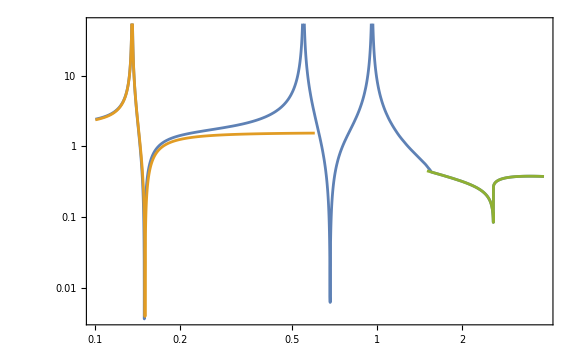

```mathematica
(*Uncomment if needed*)
(*Do[
crgval[ALPcouplingslist[[i]]]=cRGval["Gluon",10^3,ALPcouplingslist[[i]]]
,{i,1,Length[ALPcouplingslist],1}];
rgflow=Table[crgval[ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
(*The Subscript[c, γγ] coupling smoothly glued between the ChPT regime and the QCD perturbative regime*)
cγglued[ma_]=cγGluing[ma,10^3,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],crgval["ce"],crgval["cμ"],crgval["cτ"]];
(*Eq. 2.72 from https://arxiv.org/pdf/2110.10698.pdf*)
cγγEffChRotation[ma_]=If[ma<MASS["η'"],Evaluate[-((2/3(4κmatrixStandard[[1]][[1]]+κmatrixStandard[[2]][[2]]+κmatrixStandard[[3]][[3]])/.{mu->MASS["u"],md->MASS["d"],ms->MASS["s"]})-0.08)crgval["cG"]],0];
cγγNeubertLow[ma_]=cγγEffChRotation[ma]-ma^2/(MASS["π^0"]^2-ma^2)*(δval+crgval["cu"]-crgval["cd"])+(2*3*Sum[Symbol["c"<>q]*CHARGE[q]^2 LoopFactor[(4*MASS[q]^2)/ma^2],{q,{"c","b"}}]/.Table[Symbol["c"<>q]->crgval["c"<>q],{q,{"u","d","s","c","b"}}]);
cγγNeubertHigh[ma_]=Abs[(2*3*Sum[Symbol["c"<>q]*CHARGE[q]^2 LoopFactor[(4*MASS[q]^2)/ma^2],{q,{"u","d","s","c","b"}}]/.Table[Symbol["c"<>q]->crgval["c"<>q],{q,{"u","d","s","c","b"}}])+(cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,10^3,"Loop c_G"]/.Table[Symbol["c"<>q]->crgval["c"<>q],{q,{"u","d","s","c","b"}}]/.{cG->1})];
LogLogPlot[{Quiet[cγglued[ma]],If[ma<0.6,Evaluate[Abs[cγγNeubertLow[ma]]],0],If[ma>1.5,Quiet[Evaluate[Abs[cγγNeubertHigh[ma]]]],0]},{ma,0.1,3.9},Frame->True,ImageSize->Large]*)
```

#### Test 2 - various scales for the ALP universally coupled to fermions

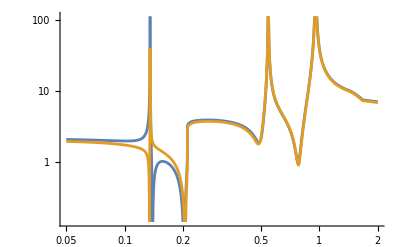

```mathematica
(*
Do[
crgval[ALPcouplingslist[[i]]]=cRGval["Fermion universal",10^3,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
rgflow=Table[crgval[ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
(*The Subscript[c, γγ] coupling smoothly glued between the ChPT regime and the QCD perturbative regime*)
cγglued1[ma_]=cγGluing[ma,10^3,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],crgval["ce"],crgval["cμ"],crgval["cτ"]];
Do[crgval[ALPcouplingslist[[i]]]=cRGval["Fermion universal",MASS["t"],ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
rgflow=Table[crgval[ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
(*The Subscript[c, γγ] coupling smoothly glued between the ChPT regime and the QCD perturbative regime*)
cγglued2[ma_]=cγGluing[ma,MASS["t"],crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],crgval["ce"],crgval["cμ"],crgval["cτ"]];
LogLogPlot[Evaluate[{cγglued1[ma],cγglued2[ma]}],{ma,0.05,2}]
*)
```

#### Test 3: comparison with 1811.03474

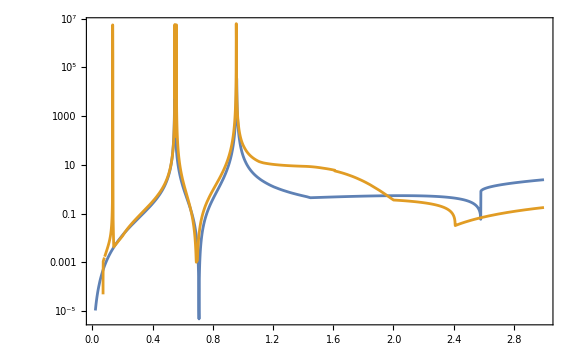

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\test\phenomenology\temp\GammaTo2gamma.txt

```mathematica
(*
cγγEff[ma_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_,"VMD"]=ruleSymbolsToNumbers[cγγEfftemp,"No π^0-η/η' mixing",2];
Do[crgval[ALPcouplingslist[[i]]]=cRGval["Gluon 1811.03474",10^3,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
cγglued1[ma_]=cγGluing[ma,10^3,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],crgval["ce"],crgval["cμ"],crgval["cτ"]];
ΓALPto2γ[ma_,fa_]=1/2 1/(8Pi)M2numeric2body["2γ",ma,fa,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],cγglued1[ma],crgval["ce"],crgval["cμ"],crgval["cτ"]] 1/(2ma);
(*Decay width into photons from Fig. S1 from https://arxiv.org/pdf/1811.03474*)
ΓALPto2γSoreq[ma_]=If[ma<=0.071,0,Evaluate[Interpolation[Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology","temp","GammaTo2gammaSoreq.txt"}],"Table"],InterpolationOrder->1][ma]]];
(*Conversion coefficients from Subscript[f, a] in https://arxiv.org/pdf/1811.03474 to Subscript[f, a] in this notebook*)
GeVtoeV=10^9;
CoefffaConversionToSoreq=GeVtoeV(32. Pi^2)^2;
LogPlot[{CoefffaConversionToSoreq*ΓALPto2γ[ma,10^3],If[ma<0.550,Evaluate[ΓALPto2γSoreq[ma]],Evaluate[ΓALPto2γSoreq[ma-0.01]]]},{ma,0.02,3},PlotRange->All,ImageSize->Large,Frame->True,FrameStyle->Directive[Thick,Black,18]]
Export[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"phenomenology","temp","GammaTo2gamma.txt"}],Table[{ma,CoefffaConversionToSoreq*ΓALPto2γ[ma,10^3]},{ma,0.02,3,0.001}],"Table"]
cγγEff[ma_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_,"VMD"]=symbolsToNumbersWidths[cγγEfftemp];
*)
```

## a->ff

### Kinematics

```mathematica
Do[
particleslist["2"<>particle]={particleFinal[particle],particleFinal[particle]};
prgroupname["2"<>particle]=If[MemberQ[listQuarks,particle]==True,"QCD jets","Leptonic"];
prclassname["2"<>particle]=If[MemberQ[listQuarks,particle]==True,"Hadronic, perturbative","Non-hadronic"];
Sfactor["2"<>particle]=1;
mLimitationMin["2"<>particle]=If[MemberQ[{"u","c","d","s","b"},particle]==True,Max[1.3,2*MASS[particleFinal[particle]]],0];
mLimitationMax["2"<>particle]=10000;
rule4MomentumConservation[expr_,"2"<>particle]:=ExpandScalarProduct[expr/.{pa->pf1+pf2}];
ruleScalarProducts[expr_,"2"<>particle]:=expr/.{ScalarProduct[pf1,pf2]->(ma^2-2 msymbolic[particleFinal[particle]]^2)/2,ScalarProduct[pf1,pa]->ma^2/2,ScalarProduct[pf2,pa]->ma^2/2,ScalarProduct[pf1,pf1]->msymbolic[particleFinal[particle]]^2,ScalarProduct[pf2,pf2]->msymbolic[particleFinal[particle]]^2};
Ncnumber["2"<>particle]=If[MemberQ[{"u","c","t","d","s","b"},particle]==True,3,1];
cfval["2"<>particle]=If[MemberQ[{"u","c","t","d","s","b"},particle]==True,cq,cl]
,{particle,{"u","d","s","c","b","t","e","μ","τ"}}]
```

### Matrix elements

```mathematica
Do[
M2body["2"<>particle]=-Symbol["c"<>particle](2msymbolic[particle])/fa SpinorUBar[pf1,msymbolic[particleFinal[particle]]].GA[5].SpinorV[pf2,msymbolic[particleFinal[particle]]]//Contract;
Mstar2body["2"<>particle]=M2body["2"<>particle]//ComplexConjugate;
M2symbolic2body["2"<>particle]=ruleKinematics[Ncnumber["2"<>particle]*FermionSpinSum[M2body["2"<>particle]*Mstar2body["2"<>particle]]/.{DiracTrace->TR}//ExpandScalarProduct//Simplify,"2"<>particle]//Simplify;
M2numeric2body["2"<>particle,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_]= symbolsToNumbersWidths[M2symbolic2body["2"<>particle]],
{particle,{"u","d","s","c","b","t","e","μ","τ"}}]
(*Matches Eq. 2.77 from https://arxiv.org/pdf/2110.10698.pdf is rescaling Subscript[c, bb] -> 2 Subscript[c, bb]*)
Assuming[ma>2*mb&&mb>0,Simplify[ΓsymbolicTemp[2,ma,"2b"]]]
```

(3 cb^2 mb^2 √(ma^2-4 mBplus^2))/(2 π fa^2)

## a->GG

### Kinematics

```mathematica
particleslist["2G"]={"G","G"};
Sfactor["2G"]=1/2;
prgroupname["2G"]="QCD jets";
prclassname["2G"]="Hadronic, perturbative";
mLimitationMin["2G"]=1.3;
mLimitationMax["2G"]=10000;
rule4MomentumConservation[expr_,"2G"]:=ExpandScalarProduct[expr/.{pa->pG1+pG2}];
ruleScalarProducts[expr_,"2G"]:=expr/.{ScalarProduct[pG1,pG2]->ma^2/2,ScalarProduct[pG1,pa]->ma^2/2,ScalarProduct[pG2,pa]->ma^2/2,ScalarProduct[pG1,pG1]->0,ScalarProduct[pG2,pG2]->0};
```

### Matrix elements

```mathematica
(*4 due to F^F = 2dA ^ 2dA*)
(*2 due to the fact that each gluon operator may annihilate each given process*)
(*1/2 due to the definition of F̃ = 1/2^F*)
M2body["2G"]=αs/(4Pi)cG*1/fa 4*2*1/2*FV[pG1,μ]*PolarizationVector[pG1,ν]FV[pG2,α]PolarizationVector[pG2,β]LeviCivita[μ,ν,α,β]//Contract;
Mstar2body["2G"]=M2body["2G"]//ComplexConjugate;
(*Factor 8: sum over colors*)
QCDcorr["2G"]=(1+83/4 αs/Pi);
M2symbolic2body["2G"]=8ruleKinematics[DoPolarizationSums[DoPolarizationSums[M2body["2G"]*Mstar2body["2G"],pG1],pG2]*QCDcorr["2G"]//ExpandScalarProduct//Simplify,"2G"]//Simplify;
M2numeric2body["2G",ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_]=symbolsToNumbersWidths[M2symbolic2body["2G"]];
Print["Decay width into gluons:"]
(*Matches Eq. 2.75 from https://arxiv.org/pdf/2110.10698.pdf*)
Assuming[ma>0,Simplify[ΓsymbolicTemp[2,ma,"2G"]/.{mG->0}]]
```

Decay width into gluons:

(αs^2 (83 αs+4 π) cG^2 ma^3)/(32 π^4 fa^2)

## a→K^0 π^0

### Kinematics

```mathematica
(*particleslist["K^0π^0"]={"K^0","π^0"};
particleslist["(K̄)^0π^0"]={"(K̄)^0","π^0"};
particleslist["K^+π^-"]={"K^+","π^-"};
particleslist["K^-π^+"]={"K^-","π^+"};
proclistKπ={"K^0π^0","(K̄)^0π^0","K^+π^-","K^-π^+"};
Do[
prgroupname[proc]="Kπ";
prclassname[proc]="Hadronic, ChPT";
,{proc,proclistKπ}];
Do[
labelList[proc]={"K","π"};
Sfactor[proc]=1;
mLimitationMin[proc]=0;
mLimitationMax[proc]=3;
momList[proc]=Symbol["p"<>(#//ToString)]&/@labelList[proc]
,{proc,proclistKπ}]
Table[With[{proc=proc},
rule4MomentumConservation[expr_,proc]:=ExpandScalarProduct[expr/.{pa->Total[momList[proc]]}];
ruleScalarProducts[expr_,proc]:=expr/.Flatten[Table[ScalarProduct[momList[proc][[i]],momList[proc][[j]]]->ScalarProduct2body[i,j],{i,1,2,1},{j,i,2,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[proc][[i]]],{i,1,2,1}];]
,{proc,proclistKπ}]*)
```

{Null,Null,Null,Null}

### Matrix elements

```mathematica
(*Do[
melelement[process]=ruleKinematics[Mdecayalp["No off-shell",particleslist[process],labelList[process]],process]//Simplify;
melelementExplicit[process]=melelement[process]/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
melementκ[process]=Simplify[D[melelementExplicit[process],κu]*κu]+Simplify[D[melelementExplicit[process],κd]*κd]//Simplify
,{process,proclistKπ}]
{#,melementκ[#]}&/@proclistKπ*)
```

(K^0π^0 | 0
(K̄)^0π^0 | 0
K^+π^- | 0
K^-π^+ | 0)